-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

{{2,1.36357},{4,2.72702},{8,5.45352},{16,10.905},{32,21.8018},{64,43.5706},{128,87.0093},{256,173.488},{512,344.833},{1024,680.927},{2048,1325.63},{4096,2497.87},{8192,4351.02},{16384,6440.55},{32768,7869.26},{65536,8581.64},{131072,8916.28},{262144,9076.2},{524288,9154.15},{1048576,9192.6},{2097152,9211.69},{4194304,9221.21}}

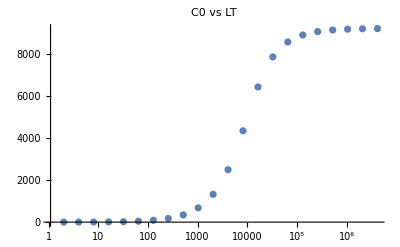

{{2,1.36357},{4,2.72702},{8,5.45352},{16,10.905},{32,21.8018},{64,43.5706},{128,87.0093},{256,173.488},{512,344.833},{1024,680.927},{2048,1325.63},{4096,2497.87},{8192,4351.02},{16384,6440.55},{32768,7869.26},{65536,8581.64},{131072,8916.28},{262144,9076.2},{524288,9154.15},{1048576,9192.6},{2097152,9211.69},{4194304,9221.21}}

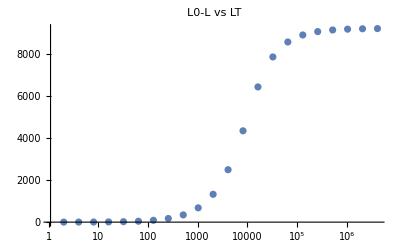

{{2,0.0000276131},{4,0.0000552253},{8,0.000110447},{16,0.000220879},{32,0.000441701},{64,0.000883167},{128,0.00176539},{256,0.00352689},{512,0.00703745},{1024,0.0140033},{2048,0.0276693},{4096,0.0535938},{8192,0.0976699},{16384,0.152524},{32768,0.193638},{65536,0.215362},{131072,0.225867},{262144,0.230958},{524288,0.233456},{1048576,0.234692},{2097152,0.235307},{4194304,0.235614}}

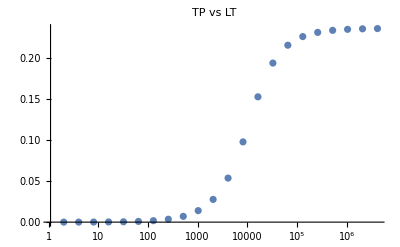

{{2,3.06802},{4,6.13574},{8,12.2703},{16,24.5361},{32,49.0536},{64,98.0332},{128,195.77},{256,390.346},{512,775.87},{1024,1532.08},{2048,2982.66},{4096,5620.19},{8192,9789.8},{16384,14491.2},{32768,17705.8},{65536,19308.7},{131072,20061.6},{262144,20421.5},{524288,20596.8},{1048576,20683.3},{2097152,20726.3},{4194304,20747.7}}

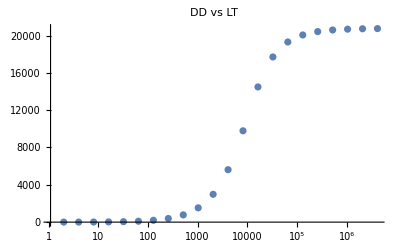

```mathematica
ZUFull={
T'[t]==-kon L[t] T[t]+koff C0[t]+k3 DD[t],
L'[t]==-kon L[t] T[t]+(koff +w)C0[t],
DD'[t]==k2 TP[t] P[t]-(k2off+k3) DD[t],
TP'[t]==-k2 TP[t] P[t]+k2off DD[t]+w C0[t],
C0'[t]==-L'[t],
P'[t]==-DD'[t]};

n=5;
(*L0=10^n;*)
initialConditionsFull={L[0]==L0,T[0]==3 10^4,C0[0]==0,DD[0]==0,TP[0]==0,P[0]==10^5};
initialConditions={L[0]->L0,T[0]->3 10^4,C0[0]->0,DD[0]->0,TP[0]->0,P[0]->10^5};
parametersFull={kon->1/10^5,koff->0.05,w->0.09,k3->0.04,k2->10^-1,k2off->0.05};tmax=300;
solutionFull=NDSolve[Join[ZUFull/.parametersFull,initialConditionsFull/.L0->10^n],{L,T,C0,DD,TP,P},{t,0,tmax},Method->{"StiffnessSwitching"},PrecisionGoal->6,AccuracyGoal->6];
Tsol=T/.solutionFull⟦1⟧;
Lsol=L/.solutionFull⟦1⟧;
C0sol=C0/.solutionFull⟦1⟧;
DDsol=DD/.solutionFull⟦1⟧;
TPsol=TP/.solutionFull⟦1⟧;
Psol=P/.solutionFull⟦1⟧;
aa=DD[0]+P[0]/.initialConditions;
Plot[{TPsol[t],(C0sol[t] w (k2off+k3))/(k2 (k3 P[0]-w C0sol[t]))/.initialConditions/.parametersFull},{t,0,tmax},PlotRange->All,(* AxesLabel->{"t (Tiempo)","C5 and S"}, *)PlotLabels->{"TP","TP como función de C0"},PlotLabel->"Gráfico de las variables vs. Tiempo",PlotStyle->{{Orange},{Blue,Dashed,Thick}}]
Plot[{Psol[t],-DDsol[t]+aa},{t,0,tmax},PlotRange->All,(* AxesLabel->{"t (Tiempo)","C5 and S"}, *)PlotLabels->{"P","P0+D0-DD"},PlotLabel->"Gráfico de las variables vs. Tiempo",PlotStyle->{{Orange},{Blue,Dashed,Thick}}]
Plot[{Psol[t],P[0]-C0sol[t] w/k3/.initialConditions/.parametersFull},{t,0,tmax},PlotRange->All,(* AxesLabel->{"t (Tiempo)","C5 and S"}, *)PlotLabels->{"P","P como función de C0"},PlotLabel->"Gráfico de las variables vs. Tiempo",PlotStyle->{{Orange},{Blue,Dashed,Thick}}]
Plot[{DDsol[t],C0sol[t] w/k3/.initialConditions/.parametersFull},{t,0,tmax},PlotRange->All,(* AxesLabel->{"t (Tiempo)","C5 and S"}, *)PlotLabels->{"D","D como función de C0"},PlotLabel->"Gráfico de las variables vs. Tiempo",PlotStyle->{{Orange},{Blue,Dashed,Thick}}]
Plot[{Tsol[t],T[0]-C0sol[t]-DDsol[t]-TPsol[t]/.initialConditions/.parametersFull},{t,0,tmax},PlotRange->All,(* AxesLabel->{"t (Tiempo)","C5 and S"}, *)PlotLabels->{"T","TT-C0-D-TP"},PlotLabel->"Gráfico de las variables vs. Tiempo",PlotStyle->{{Orange},{Blue,Dashed,Thick}}]
Plot[{C0sol[t],L[0]-Lsol[t]/.initialConditions/.parametersFull/.L0->10^n},{t,0,tmax},PlotRange->All,(* AxesLabel->{"t (Tiempo)","C5 and S"}, *)PlotLabels->{"C0","LT-L"},PlotLabel->"Gráfico de las variables vs. Tiempo",PlotStyle->{{Orange},{Blue,Dashed,Thick}}]
Plot[{C0sol[t],DDsol[t],TPsol[t]},{t,0,tmax},PlotRange->All,(* AxesLabel->{"t (Tiempo)","C5 and S"}, *)PlotLabels->{"C0","DD","TP"},PlotLabel->"Gráfico de las variables vs. Tiempo",PlotStyle->Thick]
Plot[{TPsol[t]},{t,0,tmax},PlotRange->All,(* AxesLabel->{"t (Tiempo)","C5 and S"}, *)PlotLabels->{"TP"},PlotLabel->"Gráfico de las variables vs. Tiempo",PlotStyle->Thick]
TPeqrelative[n]=TPsol[tmax]/L0;
TPeq[n]=TPsol[tmax];
C0eq[n]=C0sol[tmax];
L0=.

maxpot=22;
aabis=Table[{2^i,Evaluate[C0/.NDSolve[Join[ZUFull/.parametersFull,initialConditionsFull/.L0->2^i],{L,T,C0,DD,TP,P},{t,0,tmax},Method->{"StiffnessSwitching"},PrecisionGoal->6,AccuracyGoal->6]⟦1⟧][tmax]},{i,1,maxpot}]
ab=ListLogLinearPlot[aabis,PlotRange->All,PlotLabel->"C0 vs LT"]

maxpot=22;
aabis=Table[{2^i,L0-Evaluate[L/.NDSolve[Join[ZUFull/.parametersFull,initialConditionsFull/.L0->2^i],{L,T,C0,DD,TP,P},{t,0,tmax},Method->{"StiffnessSwitching"},PrecisionGoal->6,AccuracyGoal->6]⟦1⟧][tmax]/.L0->2^i},{i,1,maxpot}]
ab=ListLogLinearPlot[aabis,PlotRange->All,PlotLabel->"L0-L vs LT"]

maxpot=22;
aabis=Table[{2^i,Evaluate[TP/.NDSolve[Join[ZUFull/.parametersFull,initialConditionsFull/.L0->2^i],{L,T,C0,DD,TP,P},{t,0,tmax},Method->{"StiffnessSwitching"},PrecisionGoal->6,AccuracyGoal->6]⟦1⟧][tmax]},{i,1,maxpot}]
ab=ListLogLinearPlot[aabis,PlotRange->All,PlotLabel->"TP vs LT"]

maxpot=22;
aabis=Table[{2^i,Evaluate[DD/.NDSolve[Join[ZUFull/.parametersFull,initialConditionsFull/.L0->2^i],{L,T,C0,DD,TP,P},{t,0,tmax},Method->{"StiffnessSwitching"},PrecisionGoal->6,AccuracyGoal->6]⟦1⟧][tmax]},{i,1,maxpot}]
ab=ListLogLinearPlot[aabis,PlotRange->All,PlotLabel->"DD vs LT"]

(*maxpot=14;
aabis={Table[{2^i,Evaluate[L/.NDSolve[Join[ZUFull/.parametersFull,initialConditionsFull/.L0->2^i],{L,T,C0,DD,TP,P},{t,0,tmax},Method->{"StiffnessSwitching"},PrecisionGoal->6,AccuracyGoal->6]⟦1⟧][tmax]},{i,1,maxpot}],Table[{2^i,Evaluate[C0/.NDSolve[Join[ZUFull/.parametersFull,initialConditionsFull/.L0->2^i],{L,T,C0,DD,TP,P},{t,0,tmax},Method->{"StiffnessSwitching"},PrecisionGoal->6,AccuracyGoal->6]⟦1⟧][tmax]},{i,1,maxpot}]}
bb=Table[2^i,{i,1,maxpot}];
ab=ListLogLinearPlot[aabis,PlotRange->All,PlotLabel->"L and C0 vs LT"]*)
```